-Graphics-

The Wolfram Language brings together a wide range of resources concerning oceanography from the thermodynamics of sea water, ocean floor topology, tide predictions and world wide weather data coverage.

Calculate past and future tide levels based on historical values for locations across the earth or the DTU10 global ocean tide model using satellite data tide approximations of ocean water levels through the function TideData. Access WeatherData and convenience functions such as AirTemperatureData to gain information on historical weather around the world or WeatherForecastData get forecasts from the Global Forecast System and North American Mesoscale Forecast System. Use the latest research into the thermodynamics of sea water such as the Thermodynamic Equation of Seawater - 2010 through the StandardOceanData function. Through GeoElevationData and Geographics, map the world's ocean depths. Finally combine these features with the Wolfram Language's tools for analysis and visualization.

#### Predictive Tides

Calculate the first high spring tide of a month:

```mathematica
TideData[Entity["City",{"SanDiego","California","UnitedStates"}],"HighSpringTide",DateObject[{2017,5,1}]]
```

<|Time→Wed 3 May 2017 03:54:13PDT,Height→1.352 m|>

Explore how high tides adjust with the phase of the Moon:

```mathematica
hightides=TideData[Entity["City",{"NewYork","NewYork","UnitedStates"}],"HighTide",{DateObject[{2017,6,1}],DateObject[{2017,6,30}]},UnitSystem->"Imperial"];
```

```mathematica
phase=MoonPhase[{DateObject[{2017,6,1}],DateObject[{2017,6,30}],"Day"},"Icon"]["Path"][[;;;;2]];
```

```mathematica
phaseplot=DateListPlot[{{#[[1]],3.5}}&/@phase,Joined->False,PlotMarkers->({#[[2]],0.1}&/@phase),AspectRatio->1/8,FrameTicks->{Automatic,None}];
```

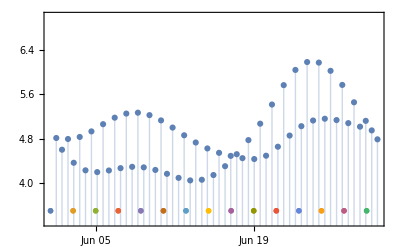

```mathematica
Show[DateListPlot[hightides,Joined->False,Filling->0],phaseplot,PlotRange->{3.3,7}]
```

Create visualizations of tidal movements across the world:

```mathematica
EmbeddedService[{"YouTube","Q3VFRTU4umw"}]
```

Null<iframe src='https://www.youtube.com/embe…der='0' allowfullscreen='true'></iframe>\r
<iframe src='https://www.youtube.com/embed/Q3VFRTU4umw?autohide=2&autoplay=0&cc_load_policy=0&color=red&controls=1&disablekb=0&enablejsapi=0&end=&fs=1&hl=&iv_load_policy=1&list=&listType=&loop=0&modestbranding=&origin=wolframcloud.com&playerapiid=&playlist=&&rel=1&showinfo=1&start=&theme=dark' id='ytplayer'  width='560' height='315' frameborder='0' allowfullscreen='true'></iframe>

#### Thermodynamics of Sea Water

Discover the density of seawater for a given salinity, pressure, and temperature:

```mathematica
StandardOceanData[Association["AbsoluteSalinity"->Quantity[35.2,("Grams")/("Kilograms")],"Pressure"->Quantity[10,"Decibars"],"Temperature"->Quantity[15,"DegreesCelsius"]],"Density"]
```

1026.05 kg/m^3

Calculate all properties for a sample of seawater:

```mathematica
Dataset[StandardOceanData[Association["PracticalSalinity"->35,"Position"->GeoPosition[{16,60}],"Pressure"->Quantity[300,"Decibars"],"Temperature"->Quantity[15,"DegreesCelsius"],"SaturationFraction"->0,"ReferencePressure"->Quantity[100,"Decibars"]]]]
```

```mathematica
StandardOceanData["Properties"]
```

{AbsolutePressure,AbsoluteSalinity,AbsoluteSalinityAnomaly,AdiabaticLapseRate,CabbelingCoefficient,ChemicalPotentialSalt,ChemicalPotentialSeaWater,ChemicalPotentialWater,Concentration,Conductivity,ConservativeMeltingPoint,ConservativeTemperature,Density,Depth,DynamicEnthalpy,Enthalpy,Entropy,FusionHeat,GibbsEnergy,GravityAcceleration,HelmholtzEnergy,InternalEnergy,IonicStrength,IsentropicCompressibility,IsobaricHeatCapacity,IsochoricHeatCapacity,MeltingPoint,Molality,OsmoticCoefficient,OsmoticPressure,PotentialDensity,PotentialDensityAnomaly,PotentialTemperature,PracticalSalinity,PreformedSalinity,ReferenceSalinity,SalineContractionCoefficient,SoundSpeed,SpecificVolume,SpecificVolumeAnomaly,ThermalExpansionCoefficient,ThermobaricCoefficient,VaporizationHeat}

#### Salinity Anomaly vs. Depth and Latitude

Discover how salinity anomaly varies with depth and latitude along 180° E longitude with seafloor elevations superimposed:

```mathematica
data=Flatten[Table[{lat,Quantity[-d,"Meters"],StandardOceanData[Association["PracticalSalinity"->35, "Position"->GeoPosition[{lat,180}],"Pressure"->Quantity[d,"Decibars"],"Temperature"->Quantity[15,"DegreesCelsius"]],"AbsoluteSalinityAnomaly"]},{lat,-85,65,5},{d,0,6000,50}],1];
```

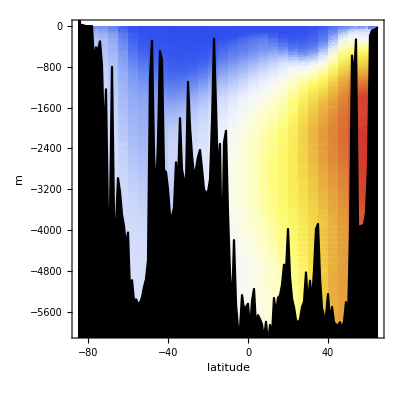

```mathematica
Show[ListDensityPlot[data,ColorFunction->"TemperatureMap",FrameLabel->{"latitude",Automatic}],ListPlot[Transpose[{Range[-85,65,1],GeoElevationData[GeoPosition[Table[{lat,180},{lat,-85,65,1}]],UnitSystem->"Metric"]}],Joined->True,Filling->Bottom,FillingStyle->Black,PlotStyle->Black]]
```

#### Ocean Floor Topography

Map ocean floors:

```mathematica
GeoGraphics[{GeoStyling["ReliefMap"],Polygon[Entity["Ocean","IndianOcean"]]},GeoBackground->None,Frame->True]
```

-Graphics-

Construct 3D models of underwater features with varying amounts of detail:

```mathematica
loihi=Entity["Volcano","Loihi"];
```

```mathematica
GraphicsRow[Table[Show[GeoElevationData[GeoDisk[loihi,Quantity[10, "Kilometers"]],Automatic,"Region",GeoZoomLevel->i],ImageSize->Medium],{i,{7,9,11}}]]
```

-Graphics-

#### World Wide Weather Data

Access weather data from stations around the world.

```mathematica
data=Table[wd=WeatherData[{y,x},"WindDirection"];If[MatchQ[wd,_Missing],{{x,y},{0,0}},{{x,y},Through[{Cos,Sin}[wd]]}],{x,-70,20,10},{y,0,70,10}];
```

Map wind patterns:

```mathematica
plot=ListStreamPlot[data,Frame->False,PlotRangePadding->0][[1]]/.a_Arrow:>Arrow[GeoPosition[Reverse/@a[[1]]]];
```

```mathematica
GeoGraphics[{{GrayLevel[.4],Arrowheads[.02],plot}},GeoRange->{{0,70},{-70,20}}]
```

-Graphics-

Examine the distribution of high temperatures for tomorrow:

```mathematica
data2=Flatten[Table[{x,y,First[WeatherForecastData[{y,x},"MaxTemperature"]["Values"]]},{x,-70,20,10},{y,0,70,10}],1];
```

```mathematica
plot2=ListDensityPlot[data2,Frame->False,PlotRangePadding->0,ColorFunction->"TemperatureMap"];
```

```mathematica
GeoGraphics[{{Opacity[.5],plot2[[1]]}},GeoRange->{{0,70},{-70,20}}]
```

-Graphics-